# Incremental Changes in Cellular Automata

## Ben Jacobsohn

## Giulio Alessandrini

## Introduction

The goal of this project is to find ways to go from specific cellular automata (CA) rules to other rules with similar behavior. Currently, the only way to effectively find behavior of CA’s is to run them over some amount of steps until clear patterns of behavior emerge. This means that the only practical way to find CA’s with particular properties is to search for them over the space of all possible CA rules. However, it is often the case that some CA’s with rules close to each other will have similar behavior. It is unclear what the relation between changing rules and changing behavior is, if there even is any. So, the aim of this project is to use machine learning methods to find any patterns that exist between changing rules and changing behavior in CA’s.

## Yee

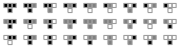
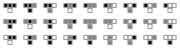
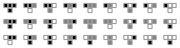
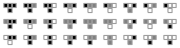
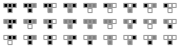
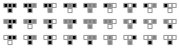
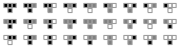
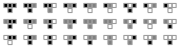
7064518774895
-Graphics-
-Graphics- | 7064518774895
-Graphics-
-Graphics- | 7064518774895
-Graphics-
-Graphics- | 7064518774895
-Graphics-
-Graphics- | 7064518774895
-Graphics-
-Graphics- | 7064518774895
-Graphics-
-Graphics- | 7064518774895
-Graphics-
-Graphics- | 7064518774895
-Graphics-
-Graphics- | 7064518774895
-Graphics-
-Graphics-
1980787118237
-Graphics-
-Graphics- | 5369941556009
-Graphics-
-Graphics- | 7346948311376
-Graphics-
-Graphics- | 7158661953722
-Graphics-
-Graphics- | 7095899834504
-Graphics-
-Graphics- | 7074979128098
-Graphics-
-Graphics- | 7068005559296
-Graphics-
-Graphics- | 7065681036362
-Graphics-
-Graphics- | 7064906195384
-Graphics-
-Graphics-
4522652946566
-Graphics-
-Graphics- | 6217230165452
-Graphics-
-Graphics- | 6782089238414
-Graphics-
-Graphics- | 7252805132549
-Graphics-
-Graphics- | 7127280894113
-Graphics-
-Graphics- | 7085439481301
-Graphics-
-Graphics- | 7061031990494
-Graphics-
-Graphics- | 7066843297829
-Graphics-
-Graphics- | 7065293615873
-Graphics-
-Graphics-

```mathematica
size = 50;
colors=3;
radius=1;
max=colors^colors^(2radius+1);
initial=RandomInteger[colors-1,size];
ruleLen=colors^(2radius+1);

getRule[]:=RandomInteger[{0,max-1}]
ruleDigits[rule_]:=IntegerDigits[rule,colors,ruleLen]
cellGrid[rule_] := CellularAutomaton[{rule,colors,radius},initial, size-1]
compressionRatio[ca_] := N[ByteCount[ca]/ByteCount[Compress[ca]], 4]
getBlocks[]:=Tuples[Reverse[Range[0,colors-1,1]],2radius+1]
countBlocks[block_,ca_]:=Total[SequenceCount[#,getBlocks[][[block]]]&/@ca]
ruleShift[rule_,block_]:=FromDigits[Mod[IntegerDigits[rule,colors,ruleLen]+SparseArray[block->1,ruleLen],colors],colors]
showRule[rule_]:=RulePlot[CellularAutomaton[{rule,colors,radius}],ImageSize->Small]
showCA[rule_]:=Column[{rule,showRule[rule],ArrayPlot[cellGrid[rule],ImageSize->Small]}]
countUses[rule_]:=countBlocks[#,cells]&/@Table[i,{i,Length[ruleDigits[rule]]}]

incrementRules[rule_,n_]:=With[{order=Ordering[countUses[rule],Ceiling[n/colors]]},
Table[NestList[ruleShift[#,order[[i]]]&,rule,colors-1],{i,Length[order]}]]

(* use foldlist to start from one replacement and replace the next least used *)


iterations=26;
rule=getRule[];
rules=incrementRules[rule,iterations];
Multicolumn[showCA[#]&/@Flatten[rules],Ceiling[iterations/colors]]
```